```mathematica
Solve[(p+1)/2-Sqrt[(p+1)^2/4+m^2 L^2]==0,m]
```

{{m→0}}

```mathematica
(p+1)/2-Sqrt[(p+1)^2/4-1/4(p+3)(p-1)]//Simplify
(p+1)/2+Sqrt[(p+1)^2/4-1/4(p+3)(p-1)]//Simplify
```

1/2 (-1+p)

(3+p)/2

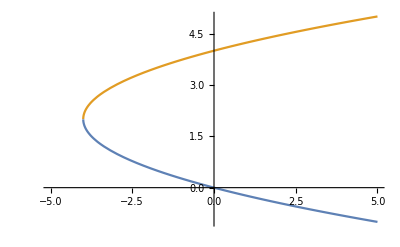

```mathematica
Plot[{(p+1)/2-Sqrt[(p+1)^2/4+ξ],(p+1)/2+Sqrt[(p+1)^2/4+ξ]}/.p->3//Evaluate,{ξ,-5,5}]
```

```mathematica
{(p+1)/2-Sqrt[(p+1)^2/4+ξ],(p+1)/2+Sqrt[(p+1)^2/4+ξ]}/.p->3/.ξ->-3
```

{1,3}

```mathematica
Series[BesselK[2,z],{z,0,1}]
```

2/z^2-1/2+O[z]^2

```mathematica
z^2/ϵ^2 BesselK[2,z p]/BesselK[2,ϵ p] 1/z^3 D[z^2/ϵ^2 BesselK[2,z p]/BesselK[2,ϵ p],z]//Simplify
```

-(BesselK[2,p z] (p z BesselK[1,p z]-4 BesselK[2,p z]+p z BesselK[3,p z]))/(2 ϵ^4 BesselK[2,p ϵ]^2)

```mathematica
Series[-(BesselK[2,p z] (p z BesselK[1,p z]-4 BesselK[2,p z]+p z BesselK[3,p z]))/(2 ϵ^4 BesselK[2,p ϵ]^2),{z,ϵ,1}]
```

-(p ϵ BesselK[1,p ϵ]-4 BesselK[2,p ϵ]+p ϵ BesselK[3,p ϵ])/(2 (ϵ^4 BesselK[2,p ϵ]))+1/(2 ϵ^5 BesselK[2,p ϵ]^2)(-4 p ϵ BesselK[1,p ϵ] BesselK[2,p ϵ]+16 BesselK[2,p ϵ]^2+p^2 ϵ^2 BesselK[2,p ϵ]^2+p^2 ϵ^2 BesselK[1,p ϵ] BesselK[3,p ϵ]-14 p ϵ BesselK[2,p ϵ] BesselK[3,p ϵ]+p^2 ϵ^2 BesselK[3,p ϵ]^2+p^2 ϵ^2 BesselK[2,p ϵ] BesselK[4,p ϵ]) (z-ϵ)+O[z-ϵ]^2

```mathematica
Series[-(ϵ BesselK[-1+ν,ϵ]-4 BesselK[ν, ϵ]+ ϵ BesselK[1+ν, ϵ])/(2 (ϵ^4 BesselK[ν, ϵ]))/.ν->2,{ϵ,0,0}]
```

-1/(2 ϵ^2)+1/4 (-EulerGamma+Log[2]-Log[ϵ])+O[ϵ]^1

```mathematica
z^2/ϵ^ν BesselK[ν,z p]/BesselK[ν,ϵ p] 1/z^3 D[z^2/ϵ^ν BesselK[ν,z p]/BesselK[ν,ϵ p],z]//Simplify
```

(ϵ^(-2 ν) BesselK[ν,p z] (-p z BesselK[-1+ν,p z]+4 BesselK[ν,p z]-p z BesselK[1+ν,p z]))/(2 BesselK[ν,p ϵ]^2)

```mathematica
Series[z^2/ϵ^ν BesselK[ν,z p]/BesselK[ν,ϵ p] 1/z^3 D[z^2/ϵ^ν BesselK[ν,z p]/BesselK[ν,ϵ p],z]//Simplify,{z,ϵ,0}]//Normal
```

(ϵ^(-2 ν) (-p ϵ BesselK[-1+ν,p ϵ]+4 BesselK[ν,p ϵ]-p ϵ BesselK[1+ν,p ϵ]))/(2 BesselK[ν,p ϵ])

```mathematica
Table[1/4 2^(2ν) Gamma[ν]^2(Assuming[Floor[(π-Arg[p]-Arg[ϵ])/(2 π)]==0,Series[(ϵ^(-2 ν) (-p ϵ BesselK[-1+ν,p ϵ]+4 BesselK[ν,p ϵ]-p ϵ BesselK[1+ν,p ϵ]))/(2 BesselK[ν,p ϵ]),{ϵ,0,0}]]//Normal//Expand)⟦-2;;-1⟧//FullSimplify,{ν,2,7}]
```

{-p^4 (Log[p/2]+Log[ϵ]),p^6 (Log[p/2]+Log[ϵ]),-p^8 (Log[p/2]+Log[ϵ]),p^10 (Log[p/2]+Log[ϵ]),-p^12 (Log[p/2]+Log[ϵ]),p^14 (Log[p/2]+Log[ϵ])}

```mathematica
(Assuming[Floor[(π-Arg[p]-Arg[ϵ])/(2 π)]==0,Series[(ϵ^(-2 ν) (-p ϵ BesselK[-1+ν,p ϵ]+4 BesselK[ν,p ϵ]-p ϵ BesselK[1+ν,p ϵ]))/(2 BesselK[ν,p ϵ])/.ν->2,{ϵ,0,0}]]//Normal//Expand)⟦-2;;-1⟧//FullSimplify
```

-1/4 p^4 (Log[p/2]+Log[ϵ])

```mathematica
(Assuming[Floor[(π-Arg[p]-Arg[ϵ])/(2 π)]==0,Series[(ϵ^(-2 ν) (-p ϵ BesselK[-1+ν,p ϵ]+4 BesselK[ν,p ϵ]-p ϵ BesselK[1+ν,p ϵ]))/(2 BesselK[ν,p ϵ]),{ϵ,0,0}]]//Normal//Expand)
```

-(2^(-1-ν) p^ν Gamma[1-ν])/(2^(-1-ν) p^ν ϵ^(2 ν) Gamma[-ν]+2^(-1+ν) p^-ν Gamma[ν])+(2^-ν p^ν Gamma[-ν])/(2^(-1-ν) p^ν ϵ^(2 ν) Gamma[-ν]+2^(-1+ν) p^-ν Gamma[ν])+(2^ν p^-ν ϵ^(-2 ν) Gamma[ν])/(2^(-1-ν) p^ν ϵ^(2 ν) Gamma[-ν]+2^(-1+ν) p^-ν Gamma[ν])-(2^(-1+ν) p^-ν ϵ^(-2 ν) Gamma[1+ν])/(2^(-1-ν) p^ν ϵ^(2 ν) Gamma[-ν]+2^(-1+ν) p^-ν Gamma[ν])

```mathematica
Integrate[p^(2ν) Exp[I p x] Log[p x],{p,0,Infinity}]
```

ConditionalExpression[(-ⅈ x)^(-1-2 ν) Gamma[1+2 ν] (-Log[-ⅈ x]+Log[x]+PolyGamma[0,1+2 ν]),Im[x]>0&&Re[ν]>-1/2]

```mathematica
2Integrate[p^(2ν+3+ϵ) Exp[I p x]/(p x),{p,0,Infinity}]
```

ConditionalExpression[(2 (-ⅈ x)^(-3-ϵ-2 ν) Gamma[3+ϵ+2 ν])/x,3+Re[ϵ+2 ν]>0&&((x∈ℝ&&2+Re[ϵ+2 ν]<0)||Im[x]>0)]

```mathematica
2 Pi^2 Integrate[(p/2)^(2 Δ-4)p^3 Exp[I p x]/(p x) Log[p ϵ],{p,0,Infinity}]
```

ConditionalExpression[ⅈ 2^(5-2 Δ) π^2 (-ⅈ x)^(-2 Δ) Gamma[-1+2 Δ] (Log[-ⅈ x]-Log[ϵ]-PolyGamma[0,-1+2 Δ]),Im[x]>0&&Re[Δ]>1/2]

```mathematica
2 Pi^2 Integrate[(p/2)^(2 Δ-4)p^3 Exp[I p x]/(p x),{p,0,Infinity}]
```

ConditionalExpression[(2^(5-2 Δ) π^2 (-ⅈ x)^(1-2 Δ) Gamma[-1+2 Δ])/x,2 Re[Δ]>1&&((x∈ℝ&&Re[Δ]<1)||Im[x]>0)]

```mathematica
(-a (x1+x2))^(-ϵ-2 (2+ν)) Gamma[4+ϵ+2 ν]
```

```mathematica
Series[((-ⅈ x)^(-3-ϵ-2 ν) Gamma[3+ϵ+2 ν])/x,{ϵ,0,1}]
```

((-ⅈ x)^(-3-2 ν) Gamma[3+2 ν])/x+(ⅈ (-ⅈ x)^(-2 ν) Gamma[3+2 ν] (Log[-ⅈ x]-PolyGamma[0,3+2 ν]) ϵ)/x^4+O[ϵ]^2

```mathematica
PolyGamma[0,2]
```

1-EulerGamma

```mathematica
Integrate[Exp[I Cos[θ] p x]Sin[θ],{θ,0,Pi}]
```

(2 Sin[p x])/(p x)

```mathematica
Table[Gamma[ν+3]/Gamma[ν](PolyGamma[0,3+2 ν]+EulerGamma),{ν,1,5}]//FullSimplify
```

{25/2,294/5,2283/14,7381/21,86021/132}